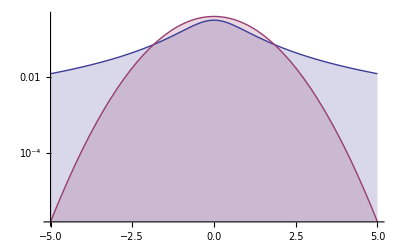

```mathematica
LogPlot[
{PDF[CauchyDistribution[0,1],x],
PDF[NormalDistribution[0,1],x]}
,{x,-5,5}, Filling->Axis]
```

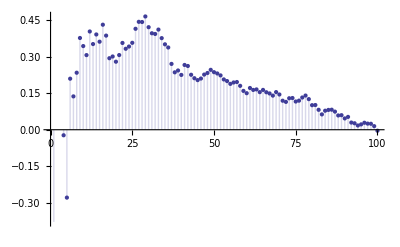

```mathematica
n=100;
𝒩=NormalDistribution[];
X=RandomVariate[𝒩,n];
m=Accumulate[X]/Range[n];
ListPlot[m,Filling->Axis]
```

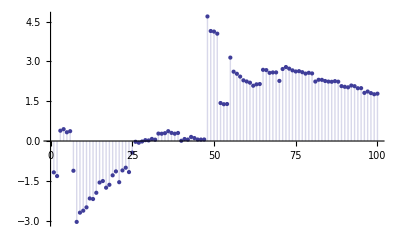

```mathematica
n=100;
𝒩=CauchyDistribution[0,2];
X=RandomVariate[𝒩,n];
m=Accumulate[X]/Range[n];
ListPlot[m,Filling->Axis]
```